```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ϵshift=0.0;
ϵ1expdata=Import["Axialstrainstress.txt","Table"];
ϵ3expdata=Import["Radialstrainstress.txt","Table"];
ϵvolexpdata=Import["Volumetricstrainstress.txt","Table"];

ϵ1expdata[[All,1]]*=1.0/100.0;
ϵ3expdata[[All,1]]*=1.0/100.0;

ϵvolexpdata= ϵ1expdata;
ϵvolexpdata [[All,1]]= 2ϵ3expdata[[All,1]]+ϵ1expdata[[All,1]];
```

```mathematica
dataϵAxial={{0.0012655430910640,4.9995206827764260},{0.0013448744558657,5.3599327937198167},{0.0014241231045212,5.7199692936051525},{0.0015033644441662,6.0799726033350341},{0.0015826051213096,6.4399729045519285},{0.0016618457381622,6.7999729319783500},{0.0017410863495251,7.1599729344757383},{0.0018203269603883,7.5199729347031177},{0.0018995675712059,7.8799729347238268},{0.0019788081820193,8.2399729347257242},{0.0020580487928324,8.5999729347259031},{0.0021372894036454,8.9599729347259025},{0.0022165300144585,9.3199729347258931},{0.0022957706252715,9.6799729347259156},{0.0023750112360846,10.0399729347259097},{0.0024542518468976,10.3999729347259020},{0.0025334924577106,10.7599729347259068},{0.0026127330685237,11.1199729347259169},{0.0026919736793367,11.4799729347259181},{0.0027712142901498,11.8399729347259175},{0.0028504549009628,12.1999729347258992},{0.0029296955117759,12.5599729347259110},{0.0030089361225889,12.9199729347259229},{0.0030881767334019,13.2799729347259170},{0.0031674173442150,13.6399729347259324},{0.0032633316927958,13.9999731121633850},{0.0033948778204314,14.3599735461363274},{0.0035268426535087,14.7199736300188011},{0.0036592016825366,15.0799736816135841},{0.0037919321004449,15.4399737300674218},{0.0039250127406235,15.7999737790709975},{0.0040584239432425,16.1599738299458622},{0.0041921474275251,16.5199738577598474},{0.0043261661771425,16.8799738981379690},{0.0044604643358154,17.2399739373635263},{0.0045950271126007,17.5999739755959084},{0.0047298406965724,17.9599740129909407},{0.0048648921792766,18.3199740496966648},{0.0050001694842873,18.6799740858500236},{0.0051356613031263,19.0399741215747227},{0.0052713570368974,19.3999741569802211},{0.0054072467430581,19.7599741921609642},{0.0055433210873199,20.1199742116517761},{0.0056795712969015,20.4799742411557446},{0.0058159891236999,20.8399742698356505},{0.0059525668042757,21.1999742977368371},{0.0060892970263951,21.5599743249022637},{0.0062261728976382,21.9199743513722858},{0.0063631879165417,22.2799743771846614},{0.0065003359460429,22.6399744023747722},{0.0066376111934875,22.9999745074129152}};


dataϵRadial={{-0.0001100300873067,4.9995206827764260},{-0.0001298628667225,5.3599327937198167},{-0.0001496750233793,5.7199692936051525},{-0.0001694853578174,6.0799726033350341},{-0.0001892955270606,6.4399729045519285},{-0.0002091056812698,6.7999729319783500},{-0.0002289158341102,7.1599729344757383},{-0.0002487259868260,7.5199729347031177},{-0.0002685361395304,7.8799729347238268},{-0.0002883462922337,8.2399729347257242},{-0.0003081564449370,8.5999729347259031},{-0.0003279665976402,8.9599729347259025},{-0.0003477767503435,9.3199729347258931},{-0.0003675869030468,9.6799729347259156},{-0.0003873970557500,10.0399729347259097},{-0.0004072072084533,10.3999729347259020},{-0.0004270173611566,10.7599729347259068},{-0.0004468275138598,11.1199729347259169},{-0.0004666376665631,11.4799729347259181},{-0.0004864478192663,11.8399729347259175},{-0.0005062579719696,12.1999729347258992},{-0.0005260681246729,12.5599729347259110},{-0.0005458782773761,12.9199729347259229},{-0.0005656884300794,13.2799729347259170},{-0.0005854985827826,13.6399729347259324},{-0.0006146318319193,13.9999731121633850},{-0.0006641519868728,14.3599735461363274},{-0.0007145856474766,14.7199736300188011},{-0.0007658912410759,15.0799736816135841},{-0.0008180296402244,15.4399737300674218},{-0.0008709640166487,15.7999737790709975},{-0.0009246596784083,16.1599738299458622},{-0.0009790839133675,16.5199738577598474},{-0.0010342058659525,16.8799738981379690},{-0.0010899963890012,17.2399739373635263},{-0.0011464279380325,17.5999739755959084},{-0.0012034744606942,17.9599740129909407},{-0.0012611112973549,18.3199740496966648},{-0.0013193150894946,18.6799740858500236},{-0.0013780636951953,19.0399741215747227},{-0.0014373361111036,19.3999741569802211},{-0.0014971124002991,19.7599741921609642},{-0.0015573736220405,20.1199742116517761},{-0.0016181017827910,20.4799742411557446},{-0.0016792797613273,20.8399742698356505},{-0.0017408912663478,21.1999742977368371},{-0.0018029207846342,21.5599743249022637},{-0.0018653535351738,21.9199743513722858},{-0.0019281754264828,22.2799743771846614},{-0.0019913730168739,22.6399744023747722},{-0.0020549334962890,22.9999745074129152}};
```

```mathematica
dataϵVolumetric = dataϵRadial;
dataϵVolumetric[[All,1]]=(dataϵAxial[[All,1]]+2 dataϵRadial[[All,1]]);
dataϵAxial[[All,1]]+=0.0006;
dataϵRadial[[All,1]]-=0.00001;

dataϵVolumetric = dataϵRadial;
dataϵVolumetric[[All,1]]=(dataϵAxial[[All,1]]+2 dataϵRadial[[All,1]]);
```

## Convert to %

```mathematica
ϵ1expdata[[All,1]]=1/100;
ϵ3expdata[[All,1]]=1/100;
ϵvolexpdata[[All,1]]=1/100;
dataϵAxial[[All,1]]=1/100;
dataϵRadial[[All,1]]=1/100;
dataϵVolumetric[[All,1]]=1/100;
```

## Plot settings

```mathematica
fontsize=18;
AText=Style[Text["Axial",{0.00725,24},{1,0}],FontSize->fontsize,Black];
RText=Style[Text["Radial",{-0.0008,24},{1,0}],FontSize->fontsize,Black];
VText=Style[Text["Volumetric",{0.004,24},{1,0}],FontSize->fontsize,Black];
txt=Graphics[{AText,RText,VText}];
```

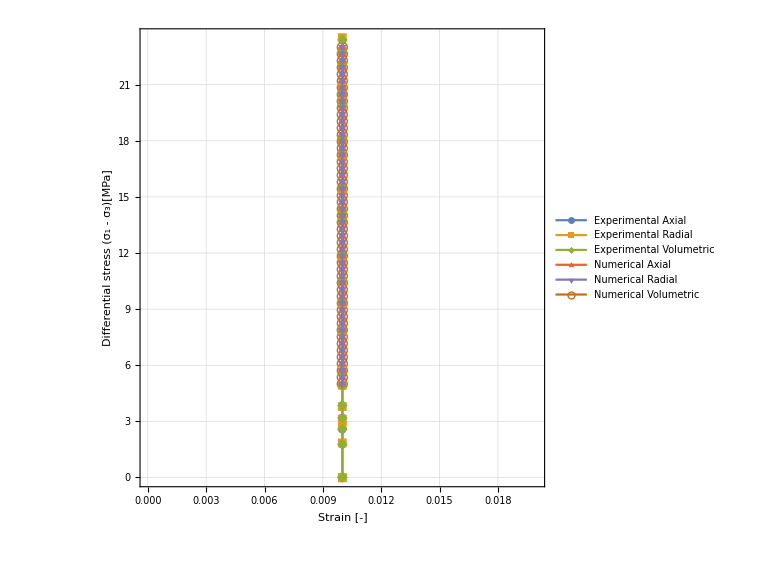

```mathematica
DeformationplotTemp=ListPlot[{ϵ1expdata,ϵ3expdata,ϵvolexpdata,dataϵAxial,dataϵRadial,dataϵVolumetric},Joined->True,AspectRatio->1, PlotMarkers->Automatic,PlotRange->All,PlotLegends->{Style["Experimental Axial",fontsize],Style["Experimental Radial",fontsize],Style["Experimental Volumetric",fontsize],Style["Numerical Axial",fontsize],Style["Numerical Radial",fontsize],Style["Numerical Volumetric",fontsize]},Frame->True,GridLines->Automatic, ImageSize->Large,FrameStyle->Directive[Black,fontsize],FrameLabel->{Style["Strain [-]",Black,fontsize],Style["Differential stress (σ_1 - σ_3)[MPa]",Black,fontsize]}]
```

```mathematica
Deformationplot=Show[DeformationplotTemp,txt];
```

```mathematica
(*Export["ElasticVerificationII.png",Deformationplot,ImageResolution->200];*)
```

## Obtaining Elastic parameters

```mathematica
model=a x +b;
fit=FindFit[ϵ1expdata[[6;;-10]],model,{a,b},x]
λ[Ey_,ν_]=(Ey ν)/((1+ν)(1-2ν));
μ[Ey_,ν_]=Ey/(2(1+ν));
```

{a→455.264,b→4.55264}

```mathematica
a
```

a

```mathematica
λ[Ey_,0.2]
```

0.277778 Ey_

## Obtaining Plastic Drucker-Prager G1:: y = 0.7463x + 12.782 R.b2 = 0.59314 G2:: y = 0.5946x + 14.035 R.b2 = 0.41776

```mathematica
adjust={α->0.5946,β->14.035};
eq1=α==Tan[45 + ϕ/2]^2//.adjust;
eq2=β==2c Tan[45 + ϕ/2]//.adjust;
sol=Solve[eq1&& eq2,{ϕ,c}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→-91.3137,c→-9.1006},{ϕ→-88.6863,c→9.1006}}

```mathematica
{eq1,eq2}//.sol[[1]]
{eq1,eq2}//.sol[[2]]
```

{True,True}

{True,True}